6.36297

0.423657

2.11829

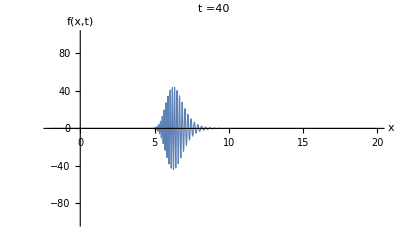

```mathematica
(* Jai Prasadh
PHY 315 HW9
Based on code written by Dr.Daniel Heinzen
*)
(*
Problem 3
a)
*)
Clear[x,k,t]
omega[k_]:=2k^0.5
k0:=40
dkrms:=5
t:=40
k[n_]:=n k0/200
f[x_,t_]:=Sum[Exp[-(k[n]-k0)^2/(4 dkrms^2)]Exp[I(omega[k[n]]t-k[n]x)],{n,0,400}]

xbar=NIntegrate[x Abs[f[x,t]]^2,{x,-2,20}]/NIntegrate[Abs[f[x,t]]^2,{x,0,20}]
dxrms=Sqrt[NIntegrate[((x-Abs[xbar])^2)*Abs[f[x,t]]^2,{x,-2,20}]/NIntegrate[Abs[f[x,t]]^2,{x,0,20}]]
dkdx = dkrms dxrms


Plot[Re[f[x,t]],{x,-2,20},PlotRange->{-20 dkrms,20 dkrms},AxesLabel->{"x","f(x,t)"},PlotStyle->Thickness[0.002],PlotLabel->StringForm["t =``",t],AxesStyle->Directive[Thickness[0.002],14]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0237794}. NIntegrate obtained 1.60087×10^-12+0. ⅈ and 6.00397×10^-11 for the integral and error estimates.

1.62632×10^-15

0.141421

0.707107

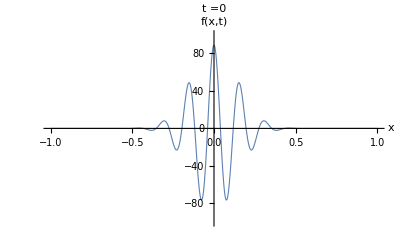

```mathematica
t:=0

xbar=NIntegrate[x Abs[f[x,t]]^2,{x,-2,20}]/NIntegrate[Abs[f[x,t]]^2,{x,0,20}]
dxrms=Sqrt[NIntegrate[((x-Abs[xbar])^2)*Abs[f[x,t]]^2,{x,-2,20}]/NIntegrate[Abs[f[x,t]]^2,{x,0,20}]]
dkdx = dkrms dxrms

Plot[Re[f[x,t]],{x,-1,1},PlotRange->{-20 dkrms,20 dkrms},AxesLabel->{"x","f(x,t)"},PlotStyle->Thickness[0.002],PlotLabel->StringForm["t =``",t],AxesStyle->Directive[Thickness[0.002],14]]
```

b) At t=0, dkrms*dxrms comes out as Sqrt(1/2), which is off from the transform-limited value of 1/2, probably since the numerical integration fails to converge at t=0.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0237794}. NIntegrate obtained 1.60087×10^-12+0. ⅈ and 6.00397×10^-11 for the integral and error estimates.

1.62632×10^-15

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0237794}. NIntegrate obtained 1.60087×10^-12+0. ⅈ and 6.00397×10^-11 for the integral and error estimates.

0.141421

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0237794}. NIntegrate obtained 1.60087×10^-12+0. ⅈ and 6.00397×10^-11 for the integral and error estimates.

0.707107

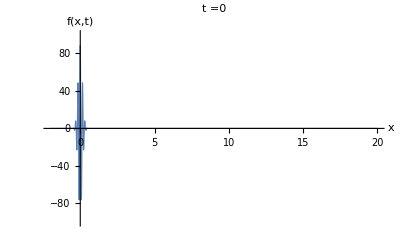

1.59074

0.143502

0.717511

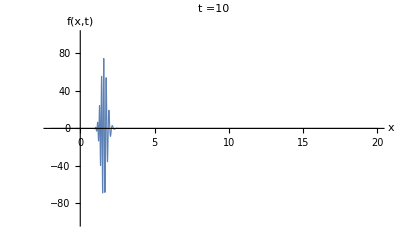

3.18149

0.228848

1.14424

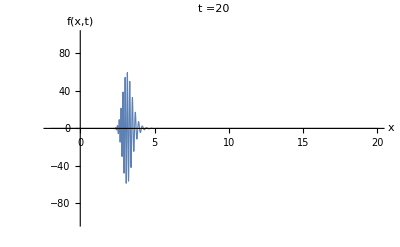

4.77223

0.324555

1.62277

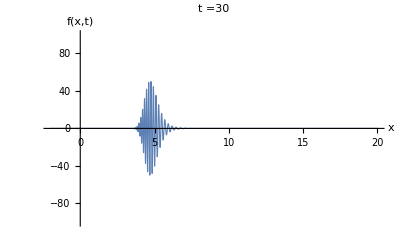

6.36297

0.423657

2.11829

-Graphics-

7.95371

0.524234

2.62117

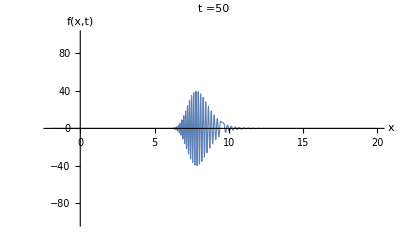

```mathematica
t:=0
xbar
dxrms
dkdx

Plot[Re[f[x,t]],{x,-2,20},PlotRange->{-20 dkrms,20 dkrms},AxesLabel->{"x","f(x,t)"},PlotStyle->Thickness[0.002],PlotLabel->StringForm["t =``",t],AxesStyle->Directive[Thickness[0.002],14]]

t:=10
xbar
dxrms
dkdx

Plot[Re[f[x,t]],{x,-2,20},PlotRange->{-20 dkrms,20 dkrms},AxesLabel->{"x","f(x,t)"},PlotStyle->Thickness[0.002],PlotLabel->StringForm["t =``",t],AxesStyle->Directive[Thickness[0.002],14]]

t:=20
xbar
dxrms
dkdx

Plot[Re[f[x,t]],{x,-2,20},PlotRange->{-20 dkrms,20 dkrms},AxesLabel->{"x","f(x,t)"},PlotStyle->Thickness[0.002],PlotLabel->StringForm["t =``",t],AxesStyle->Directive[Thickness[0.002],14]]

t:=30
xbar
dxrms
dkdx

Plot[Re[f[x,t]],{x,-2,20},PlotRange->{-20 dkrms,20 dkrms},AxesLabel->{"x","f(x,t)"},PlotStyle->Thickness[0.002],PlotLabel->StringForm["t =``",t],AxesStyle->Directive[Thickness[0.002],14]]

t:=40
xbar
dxrms
dkdx

Plot[Re[f[x,t]],{x,-2,20},PlotRange->{-20 dkrms,20 dkrms},AxesLabel->{"x","f(x,t)"},PlotStyle->Thickness[0.002],PlotLabel->StringForm["t =``",t],AxesStyle->Directive[Thickness[0.002],14]]

t:=50
xbar
dxrms
dkdx

Plot[Re[f[x,t]],{x,-2,20},PlotRange->{-20 dkrms,20 dkrms},AxesLabel->{"x","f(x,t)"},PlotStyle->Thickness[0.002],PlotLabel->StringForm["t =``",t],AxesStyle->Directive[Thickness[0.002],14]]
```

```mathematica
Clear[t]
funxbar[t_]:=NIntegrate[x Abs[f[x,t]]^2,{x,-2,20}]/NIntegrate[Abs[f[x,t]]^2,{x,0,20}]
fundxrms[t_]:=Sqrt[NIntegrate[((x-Abs[funxbar[t]])^2)*Abs[f[x,t]]^2,{x,-2,20}]/NIntegrate[Abs[f[x,t]]^2,{x,0,20}]]
Normal[Re[fundxrms[t]]]
```

NIntegrate::inumr: The integrand Abs[(1.12535×10^-7+0. ⅈ)+ⅇ^(-16+ⅈ (Times[«2»]+Times[«2»]))+«47»+ⅇ^(-5776/625+ⅈ (Times[«2»]+Times[«2»]))+«351»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,20}}.

NIntegrate::inumr: The integrand x Abs[(1.12535×10^-7+0. ⅈ)+ⅇ^(-16+ⅈ Plus[«2»])+ⅇ^(-39601/2500+ⅈ Plus[«2»])+«45»+ⅇ^(-23409/2500+ⅈ Plus[«2»])+ⅇ^(-5776/625+ⅈ Plus[«2»])+«351»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-2,20}}.

NIntegrate::inumr: The integrand Abs[(1.12535×10^-7+0. ⅈ)+ⅇ^(-16+ⅈ (Times[«2»]+Times[«2»]))+«47»+ⅇ^(-5776/625+ⅈ (Times[«2»]+Times[«2»]))+«351»]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,20}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
approxdxrms[t_]:=Sqrt[(0.1435021028285533)^2 + ((0.5 k0^(-1.5))(0.1435021028285533^-1)t)^2]

Show[Plot[Re[fundxrms[t]],{t,5, 20},PlotRange->{0,10},PlotLegends->{"delta xrms(t)"}],Plot[approxdxrms[t],{t,5, 20},PlotRange->{0,10},PlotLegends->{"approximation"}],AxesLabel->{"Time (s)","RMS width (m^-1)"}]
```

$Aborted